# Code for generating Fig. 1 of the paper

#### This script reproduces Figure 1 in the paper: [1] “Temperature Overloads in Power Grids Under Uncertainty: a Large Deviations Approach”, Tommaso Nesti, Jayakrishnan Nair and Bert Zwart, accepted for publication in IEEE Transactions on Control of Network Systems. It makes use of the MATPOWER test case ‘case14.mpc’: [2] http://www.pserc.cornell.edu/matpower/docs/ref/matpower5.0/case14.html

```mathematica
Code for Fig 1 a,b
```

```mathematica
Edges=20;
Nodes=14;
StochNodes=2;
(*DEFINITION OF EDGES-VERTEX MATRIX A-------------------------------*)
Amat=Table[0,{Edges},{Nodes}];

(* Original node ordering is [1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14].

We model nodes 2 and 13 as stochastic nodes. According to our model definition in Eq II.4, stochastic nodes should immediately follows the slack node (node 1), i.e. node ordering should be [1, 2, 13, 3, 4, 5, 6, 7 ,8 ,9 ,10, 11, 12, 14]. Therefore, we relabel nodes as follows:

Original_label  New_label
1                1 
2                2
3                4
4                5
5                6
6                7 
7                8
8                9
9                10
10               11
11               12
12               13
13               3
14               14

In the following, we construct the edge-vertex adjacent matrix based on the data in case14.mpc using the new labels and following lexicographical order (based on the new labels).
The edgelists, according to the original and the new nodal labelling, is as follows:

(* new_edge_ordering   new_edge  original_edge    original_edge_ordering          
		1:            {1,2}      {1,2}           1
		2:            {1,6}      {1,5}           2
		3:            {2,4}      {2,3}           3     
		4:            {2,5}      {2,4}           4
		5:            {2,6}      {2,5}           5
		6:            {3,7}      {13,6}R         13
		7:            {3,13}     {13,12}R        19
		8:            {3,14}     {13,14}         20
		9:            {4,5}      {3,4}           6
		10:           {5,6}      {4,5}           7
		11:           {5,8}      {4,7}           8
		12:           {5,10}     {4,9}           9
		13:           {6,7}      {5,6}           10 
		14:           {7,12}     {6,11}          11
		15:           {7,13}     {6,12}          12
		16:           {8,9}      {7,8}           14
		17:           {8,10}     {7,9}           15   
		18:           {10,11}    {9,10}          16
		19:          {10,14}     {9,14}          17
		20:          {11,12}     {10,11}         18       
*)
The new ordering applies to every component of the model (i.e. betas, mu etc...)
*)

(*index 1 gives the entries of matrix A which must be set to 1. First component ranges form 1 to 20 (lines), second component ranges from 1 to 13 (nodes), and it is the sending node for that edge*)

index1=  {  { 1,1},{2,1},
		{3,2},{4,2},{5,2},
                  {6,3},{7,3},{8,3},
		{9,4},
		{10,5},{11,5},{12,5},
		{13,6},
		{14,7},{15,7},
		{16,8},{17,8},
		{18,10},{19,10},
		{20,11}
                };

(*index 2 gives the entries of matrix A which must be set to -1. First component ranges form 1 to 20 edges), second component ranges from 1 to 13 (nodes), and it is the receiving node for that edge*)

index2=  {  {1,2},{2,6},
		{3,4},{4,5},{5,6},
                  {6,7},{7,13},{8,14},
		{9,5},
		{10,6},{11,8},{12,10},
		{13,7},
		{14,12},{15,13},
		{16,9},
		{17,10},
		{18,11},{19,14},
		{20,12}
                };



Amat=ReplacePart[Amat,index1->1];
Amat=ReplacePart[Amat,index2->-1];

(*edge list--------------------------------*)

index3=  {{1,2},{1,6},
		{2,4},{2,5},{2,6},
                  {3,7},{3,13},{3,14},
		{4,5},
		{5,6},{5,8},{5,10},
		{6,7},
		{7,12},{7,13},
		{8,9},{8,10},
		{10,11},{10,14},
		{11,12}
                };


(*************************************)
(*betas*)
Betamat2={15.2631,
4.2350,
4.7819,
5.1158,
5.1939,
(*betas for edges starting from new node '3' (old node 13) *)
6.1028,
2.2520,
2.3150,
(*---*)
5.0688,
21.5786,
4.7819,
1.7980,
3.9679,
4.0941,
3.1760,
5.6770,
9.0901,
10.3654,
3.0291,
4.4029};

Dmat=DiagonalMatrix[Betamat2];
count=1;
Betamat=Table[0,{Nodes},{Nodes}];

For[i=1,i≤Nodes-1,i++,
For[j=1,j≤Nodes,j++,

If  [count≤20&&{i,j}==index3[[count]],
(Betamat[[i,j]]=Betamat2[[count]];
count=count+1),
(Unevaluated[Sequence[]] )
]
]
]

Betamat=Betamat+Transpose[Betamat];
MatrixForm[Betamat2];
(*Construction of admittance matrix B---------------------*)
Bmat=Table[0,{Nodes},{Nodes}];
Sumbeta=Table[0,{Nodes}];
For[i=1,i≤Nodes,i++,
For[k=1,k≤Nodes,k++,
If[k≠ i,{Sumbeta[[i]]+=Betamat[[i,k]]},Sumbeta[[i]]=Sumbeta[[i]]];
] 
For[j=1,j≤Nodes,j++,
Bmat[[i,j]]=If[i≠j,-Betamat[[i,j]],Sumbeta[[i]]];
]
]

(*Construction of B hat*)
Btriang=Bmat[[2;;Nodes,2;;Nodes]];
Btrianginv=Inverse[Btriang];
Bhat=ArrayFlatten[{{0,0},{0,Btrianginv}}];

(* Construction of matrices C,C_D, C^+ *)
Ctilde=Dmat.Amat.Bhat;
Cmat=Ctilde[[1;;Edges,2;;3]];
CDmat=Ctilde[[1;;Edges,4;;14]];
Cplus=Inverse[Transpose[Cmat].Cmat].Transpose[Cmat];

(* mu *)
mudet={-94.2,-47.8,-7.6,  -11.2,0,0,-29.5,-9,-3.5,-6.1,-14.9};
mustoch={18.3,-13.5};

(* Sign function*)
S[x_]:=Piecewise[{{1,0≤x}},-1];

Lsquared=10*IdentityMatrix[2];
CCmat=Drop[Cmat,{16}];
CCDmat=Drop[CDmat,{16}];
(* we remove line (8,9) (line (7,8) in the old labelling), because it does not depend on x and y. From now on, the edge list is as follows:

(* new_edge_ordering   new_edge  original_edge        
		1:            {1,2}      {1,2}           
		2:            {1,6}      {1,5}           
		3:            {2,4}      {2,3}                
		4:            {2,5}      {2,4}           
		5:            {2,6}      {2,5}           
		6:            {3,7}      {13,6}R         
		7:            {3,13}     {13,12}R        
		8:            {3,14}     {13,14}         
		9:            {4,5}      {3,4}           
		10:           {5,6}      {4,5}           
		11:           {5,8}      {4,7}           
		12:           {5,10}     {4,9}           
		13:           {6,7}      {5,6}            
		14:           {7,12}     {6,11}          
		15:           {7,13}     {6,12}         
-----------------------------
		'16':           {8,10}     {7,9}              
	   '17':           {10,11}    {9,10}          
	   '18':           {10,14}    {9,14}          
	   '19':           {11,12}    {10,11}                
*)
*)


vinit=CCmat.{18.3,-13.5}+CCDmat.mudet;
alpha=1.5;
CCmat=CCmat/(alpha*vinit);
CCDmat=CCDmat/(alpha*vinit);
v[x_,y_]:=CCmat.{18.3,-13.5}+CCDmat.{-94.2,-47.8,-7.6,x,0,0,y,-9,-3.5,-6.1,-14.9};
(* In terms of Eq. II.5, this is equal to 
C*X(t)+ C_D*mu_det, 
  where:
X(t) = stochastic power injections (nodes 2,3 in new labelling, nodes 2,13 in original labelling) mudet = deterministic power injections (nodes 4,5,6,7,8,9,10,11,12,13,14 in new labelling, nodes 3,4,5,6,7,8,9,10,11,12,14 in original labelling)

The values are based on column "Pd" in mpc.bus and column "Pg" in mpc.gen
*)


prod1=Lsquared.Transpose[CCmat];
pprod1=Lsquared.Transpose[CCmat];
prod2=CCmat.prod1;
prodvec=Diagonal[prod2];
pprodvec=prodvec;
Denomin=DiagonalMatrix[prodvec];
DDenomin=Denomin; 
DDenomininv=Inverse[DDenomin];


psi[x_,y_]:=DDenomininv.((Map[S,v[x,y]]-v[x,y])^2)
Minimo[x_,y_]:=Min[psi[x,y]];
P[x_,y_]:=(Max[Map[Abs,v[x,y]]]<1);
Pall[x_,y_]:=(Max[Map[Abs,v[x,y]]]<1);
pos[x_,y_]:=FirstPosition[psi[x,y],Minimo[x,y]]
R[x_,y_]:=CCmat.(pprod1[[All,pos[x,y][[1]]]])(1/pprodvec[[pos[x,y][[1]]]]);
```

### Fig 1a)

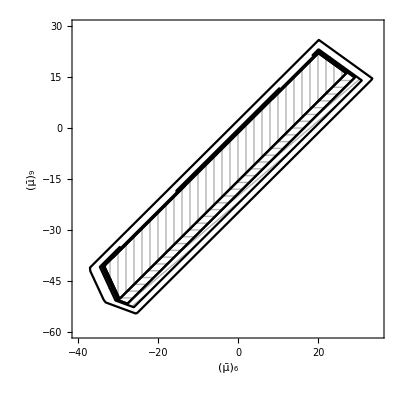

```mathematica
(* T=1,γi=1,li=10,.0f=0.25 and τ=0.5. *)

tau=0.5;
T=1;
gamma=1;
eps=0.25;
p=10^-4;

COST1[gamma_,T_]:=gamma/(1-Exp[-2gamma*T])
COST2[eps_,p_]:=eps*Log[1/p];
COST3[gamma_,tau_]:=2*gamma*tau
COST4[gamma_,tau_]:=1-Exp[-gamma*T]
C1=COST1[gamma,T];
C2=COST2[eps,p];
C3=COST3[gamma,tau];
C4=COST4[gamma,tau];

alphaa[x_,y_]:=Sqrt[(1-v[x,y]^2*Exp[-T/tau])/(1-Exp[-T/tau])];
Lowerbound[x_,y_]:=MapThread[Min,{(gamma*(alphaa[x,y]-v[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T])),
                                                       (gamma*(-alphaa[x,y]-v[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T]))}];
ICURRENT[x_,y_]:=C1*Minimo[x,y];
ITAYLORmod3[x_,y_]:=ICURRENT[x,y]*(1+C3);



Show[RegionPlot[P[x,y],{x,-40,35},{y,-60,30},MaxRecursion->4,PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ICURRENT[x,y]≥C2,{x,-40,35},{y,-60,30},MaxRecursion->4,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12}FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&Min[Lowerbound[x,y]]≥C2&&ICURRENT[x,y]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ITAYLORmod3[x,y]≥C2&&Min[Lowerbound[x,y]]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}] 
]
```

### Draw again Fig 1a by defining the polygon’s coordinates based on the output of previous cell, and use meshing to shade interiors. This is just for aesthetic reasons.

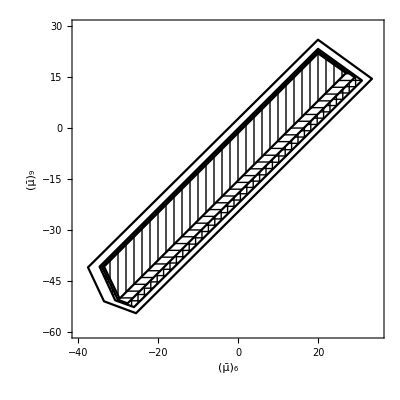

```mathematica
P0=Polygon[{{0,0},{0,0}}];
P1=Polygon[{{20,26},{33.5,14.5},{-25.5,-54.5},{-33.5,-51},{-37.5,-41}}];
Ptaylor=Polygon[{{20,23.3},{31,14},{-26,-52.7},{-30.7,-50.7},{-34.6,-40.8}}];
Plb=Polygon[{{20,22.6},{29.2,14.9},{-27.6,-51.6},{-30,-50.6},{-34,-40.9}}];
Pcurrent=Polygon[{{20,22},{27,16.2},{-29.6,-50.2},{-33.5,-40.8}}];

(*Define mesh markers *)
MeshMarker[a_,b_]:=RegionPlot[True,{x,-1,1},{y,-1,1},Frame->False,Mesh->{a,b},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];

MeshMarker1=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Black,Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];

MeshMarker2=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#2 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];
MeshMarker12=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 -#2 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];
MeshMarker21=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1+#2 &},Mesh->{Range[-3,3,0.75]},MeshStyle->{Thickness[0.005]},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];


(*define polygonal regions *)
h0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]}
];

h1=RegionPlot[P1,BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{Subscript[ℛ, det]},
LegendMarkers->MeshMarkerWhite,LegendMarkerSize->30]];

htaylor=RegionPlot[Ptaylor,Mesh->{40,40},
MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^(TL)},
LegendMarkers->MeshMarker[4,4],LegendMarkerSize->30]];

hlb=RegionPlot[Plb,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^(LB)},
LegendMarkers->MeshMarker2,LegendMarkerSize->30]];

hcurrent=RegionPlot[Pcurrent,MeshFunctions->{#1&},
Mesh->{Range[-60,50,2]},
MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^{(cur)}},
LegendMarkers->MeshMarker1,LegendMarkerSize->30]];
Show[h0,h1,htaylor,hlb,hcurrent]
```

### Fig 1b)

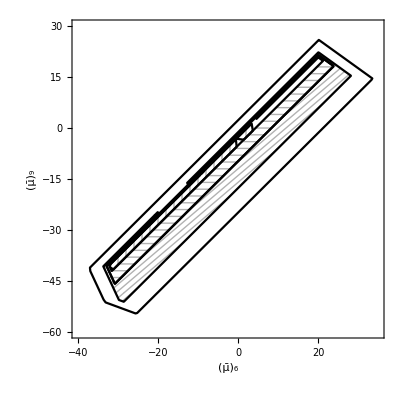

```mathematica
tau=0.5;
T=1;
gamma=1;
eps=0.25;
p=10^-7;

COST1[gamma_,T_]:=gamma/(1-Exp[-2gamma*T])
COST2[eps_,p_]:=eps*Log[1/p];
COST3[gamma_,tau_]:=2*gamma*tau;
COST4[gamma_,tau_]:=1-Exp[-gamma*T]
C1=COST1[gamma,T];
C2=COST2[eps,p];
C3=COST3[gamma,tau];
C4=COST4[gamma,tau];

alphaa[x_,y_]:=Sqrt[(1-v[x,y]^2*Exp[-T/tau])/(1-Exp[-T/tau])];
Lowerbound[x_,y_]:=MapThread[Min,{(gamma*(alphaa[x,y]-v[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T])),
                                                       (gamma*(-alphaa[x,y]-v[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T]))}];
ICURRENT[x_,y_]:=C1*Minimo[x,y];
ITAYLORmod3[x_,y_]:=ICURRENT[x,y]*(1+C3);



Show[RegionPlot[P[x,y],{x,-40,35},{y,-60,30},MaxRecursion->4,PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ICURRENT[x,y]≥C2,{x,-40,35},{y,-60,30},MaxRecursion->4,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12}FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&Min[Lowerbound[x,y]]≥C2&&ICURRENT[x,y]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ITAYLORmod3[x,y]≥C2&&Min[Lowerbound[x,y]]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}]
]
```

#### Draw again the capacity regions by defining the polygon’s coordinates based on the output of previous cell, and use mesh to shade interiors. This is just for aesthetic reasons.

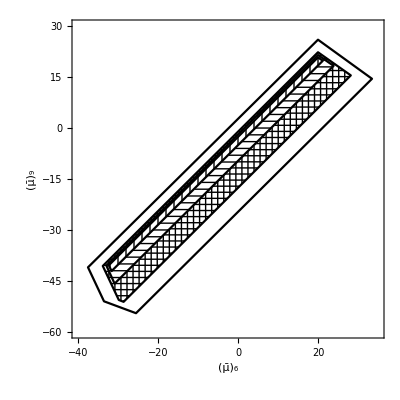

```mathematica
P0=Polygon[{{0,0},{0,0}}];
P1=Polygon[{{20,26},{33.5,14.5},{-25.5,-54.5},{-33.5,-51},{-37.5,-41}}];
Ptaylor=Polygon[{{20,22.3},{28.2,15.5},{-28.6,-51.15},{-29.8,-50.6},{-33.8,-40.6}}];
Plb=Polygon[{{20,21.5},{23.9,18.3},{-30.85,-45.8},{-32.9,-40.5}}];
Pcurrent=Polygon[{{20,20.8},{21.2,19.8},{-31.6,-42.1},{-32.3,-40.4}}];


MeshMarker[a_,b_]:=RegionPlot[True,{x,-1,1},{y,-1,1},Frame->False,Mesh->{a,b},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];

MeshMarker1=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Black,Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];

MeshMarker2=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#2 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];
MeshMarker12=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 -#2 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,MeshStyle->{Thickness[0.05]},PlotStyle->White,BoundaryStyle->Black];
MeshMarker21=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1+#2 &},Mesh->{Range[-3,3,0.75]},MeshStyle->{Thickness[0.005]},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];



h0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]}
];

h1=RegionPlot[P1,BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{Subscript[ℛ, det]},
LegendMarkers->MeshMarkerWhite,LegendMarkerSize->30]];

htaylor=RegionPlot[Ptaylor,Mesh->{40,40},
MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^(TL)},
LegendMarkers->MeshMarker[4,4],LegendMarkerSize->30]];

hlb=RegionPlot[Plb,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^(LB)},
LegendMarkers->MeshMarker2,LegendMarkerSize->30]];

hcurrent=RegionPlot[Pcurrent,MeshFunctions->{#1&},
Mesh->{Range[-60,50,2]},
MeshStyle->{Thickness[0.0025]},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{OverTilde[ℛ]^{(cur)}},
LegendMarkers->MeshMarker1,LegendMarkerSize->30]];
Show[h0,h1,htaylor,hlb,hcurrent]
```

```mathematica
Fig 1c)
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

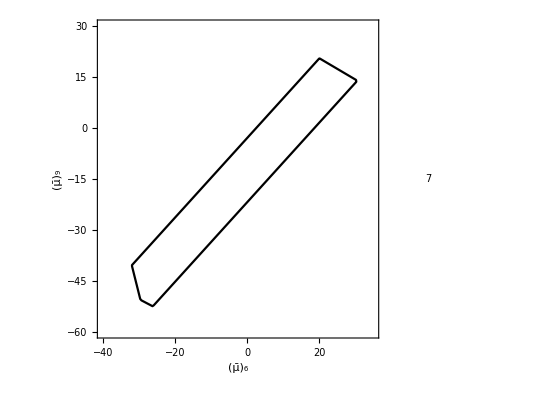

8

-Graphics-

9

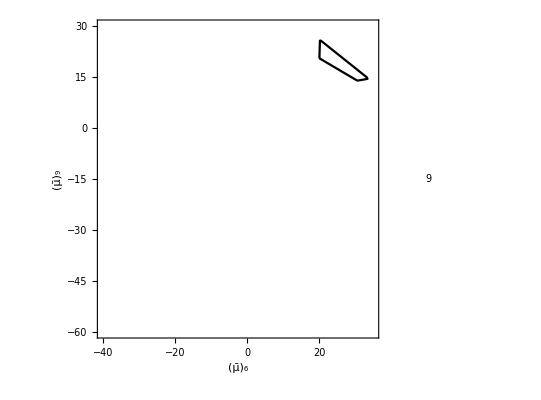

10

-Graphics-

11

-Graphics-

12

-Graphics-

13

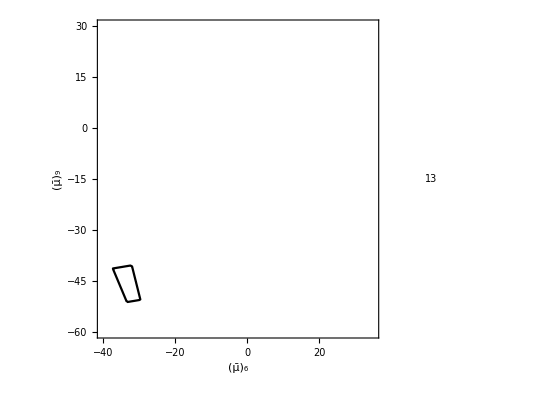

14

-Graphics-

15

-Graphics-

16

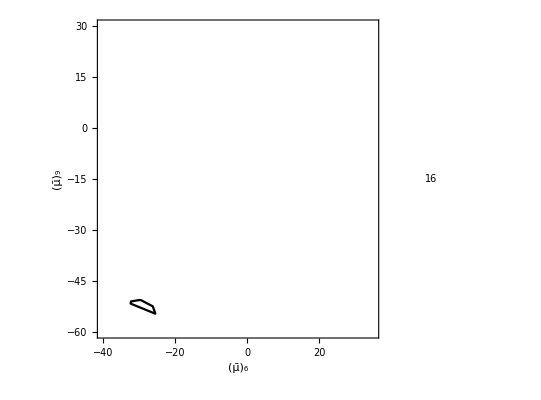

17

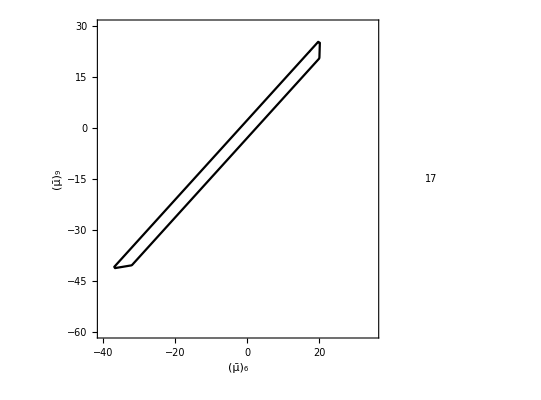

18

-Graphics-

19

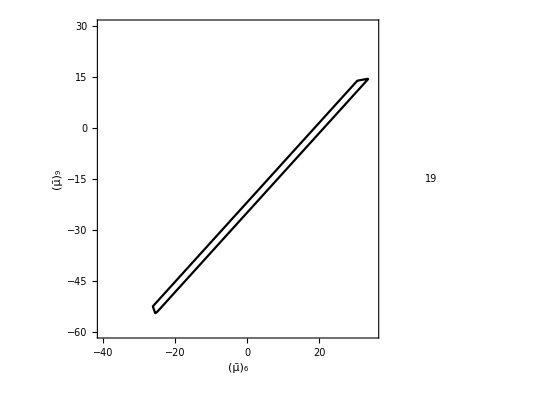

```mathematica
(* Compute regions S_k, as defined in Eq (V.2)*)


listplot= {};
For[i=1,i<20,i++,
Print[i];
g=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==i
                   },{x,-40,35},{y,-60,30},PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->2,
BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]},
 PlotLegends->{i}];
AppendTo[listplot,g];
Print[g]
]
```

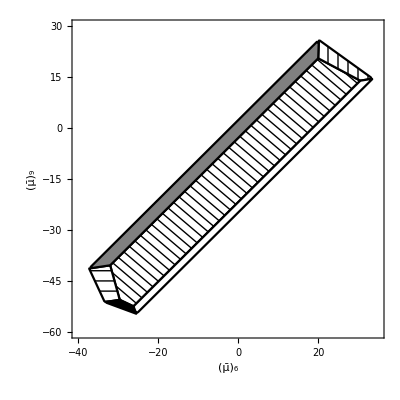

```mathematica
(* The most vulnerable liens are the ones marked with a *: 

   new_edge_ordering   new_edge  original_edge        
		1:            {1,2}      {1,2}           
		2:            {1,6}      {1,5}           
		3:            {2,4}      {2,3}                
		4:            {2,5}      {2,4}           
		5:            {2,6}      {2,5}           
		6:            {3,7}      {13,6}R         
		7:            {3,13}     {13,12}R  *      
		8:            {3,14}     {13,14}         
		9:            {4,5}      {3,4} *          
		10:           {5,6}      {4,5}           
		11:           {5,8}      {4,7}          
		12:           {5,10}     {4,9}           
		13:           {6,7}      {5,6}     *       
		14:           {7,12}     {6,11}          
		15:           {7,13}     {6,12}         
-----------------------------
		'16':           {8,10}     {7,9}  *            
		'17':           {10,11}    {9,10}  *        
		'18':          {10,14}     {9,14}          
		'19':          {11,12}     {10,11}   *             
*)

(* define mesh markers*)
MeshMarker[a_,b_]:=RegionPlot[True,{x,-1,1},{y,-1,1},Frame->False,Mesh->{a,b},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];

MeshMarker1=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 &},Mesh->{Range[-3,3,0.75]},ImageSize->10,
MeshStyle->{Thick},PlotStyle->White,BoundaryStyle->Black];

MeshMarker2=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#2 &},Mesh->{Range[-3,3,0.75]},MeshStyle->{Thick},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];

MeshMarker12=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1 -#2 &},Mesh->{Range[-3,3,0.75]},MeshStyle->{Thick},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];

MeshMarker21=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,MeshFunctions->{#1+#2 &},Mesh->{Range[-3,3,0.75]},MeshStyle->{Thick},ImageSize->10,PlotStyle->White,BoundaryStyle->Black];

MeshMarkerBlack=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,ImageSize->10,PlotStyle->Black,BoundaryStyle->Black];

MeshMarkerGray=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,ImageSize->10,PlotStyle->Gray,BoundaryStyle->Black];

MeshMarkerWhite=RegionPlot[True,{x,-2,2},{y,-2,2},Frame->False,ImageSize->10,PlotStyle->White,BoundaryStyle->Black];



(* Plot Fig 1c)*)
P0=Polygon[{{0,0},{0,0}}];
h0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},PlotStyle->White,BoundaryStyle->Black,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]}];

g1=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==7
                   },{x,-40,35},{y,-60,30},
PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->2,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
MeshFunctions->{#1+#2&},Mesh->{Range[-80,50,3]},MeshStyle->{Thick},
PlotLegends->SwatchLegend[{1},{"S_(12, 13)"},
LegendMarkers->MeshMarkerGray,LegendMarkerSize->30]];


g2=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==9
                   },{x,-40,35},{y,-60,30},
PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->2,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
MeshFunctions->{#1&},Mesh->{Range[-60,50,2.5]},MeshStyle->{Thick},
PlotLegends->SwatchLegend[{1},{"S_(3, 4)"},
LegendMarkers->MeshMarker1,LegendMarkerSize->30]];

g3=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==13
                   },{x,-40,35},{y,-60,30},
PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->4,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
MeshFunctions->{#2&},Mesh->{Range[-60,50,3]},MeshStyle->{Thick},
PlotLegends->SwatchLegend[{1},{"S_(5, 6)"},
LegendMarkers->MeshMarker2,LegendMarkerSize->30]];

g4=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==16
                   },{x,-40,35},{y,-60,30},
PlotStyle->Black,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->4,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
Mesh->{0,0},PlotLegends->SwatchLegend[{1},{"S_(7, 9)"},
LegendMarkers->MeshMarkerBlack,LegendMarkerSize->30]];

g5=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==17
                   },{x,-40,35},{y,-60,30},
PlotStyle->Gray,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->2,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{"S_(9, 10)"},
LegendMarkers->MeshMarkerGray,LegendMarkerSize->30]];



g6=RegionPlot[{
P[x,y]&&pos[x,y][[1]]==19
                   },{x,-40,35},{y,-60,30},PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->2,
BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->16,FontWeight->Bold],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14,FontWeight->Bold]},
PlotLegends->SwatchLegend[{1},{"S_(10, 11)"},
LegendMarkers->MeshMarkerWhite,LegendMarkerSize->30]];

Show[h0,g1,g2,g3,g4,g5,g6]
```

```mathematica
Fig. 1d
```

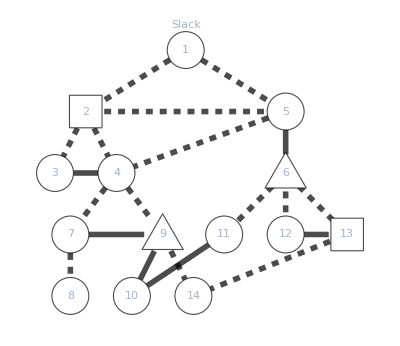

```mathematica
Graph[{1<->2,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5,4<->7,4<->9,5<->6,6<->11,6<->12,6<->13,7<->8,7<->9,9<->10,9<->14,10<->11,12<->13,13<->14},VertexLabels->{1->Placed[{1,Slack},{Center,Above}],2->Placed[{2},{Center}],3->Placed[{3},{Center}],4->Placed[{4},{Center}],5->Placed[{5},{Center}],6->Placed[{6},{Center}],7->Placed[{7},{Center}],8->Placed[{8},{Center}],9->Placed[{9},{Center}],10->Placed[{10},{Center}],11->Placed[{11},{Center}],12->Placed[{12},{Center}],13->Placed[{13},{Center}],Placed[{14},{Center}]},VertexSize->0.6,VertexStyle->{1|2|9|13|6|0|3|4|5|7|8|10|11|12|14->White},VertexShapeFunction->{2->"Square",13->"Square",6->"Triangle",9->"Triangle"},EdgeStyle->{3<->4|12<->13| 5<->6|7<->9|9<->10|10<->11->Black,Thickness[0.01],1<->5|2<->3|4<->7|4<->5|1<->2|2<->5|2<->4|4<->9|6<->11|6<->12|6<->13|7<->8|9<->14|13<->14->{Black,Dashed,Thick}},GraphLayout->"LayeredDrawing"]
```